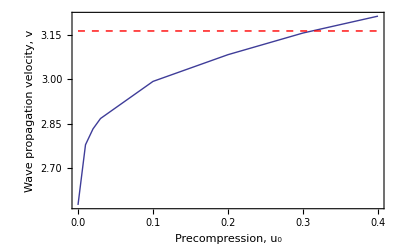

```mathematica
v={2.5773,2.7797,2.8330,2.8679,2.9927,3.0826,3.1554,3.2122};
u0={0,0.01,0.02,0.03,0.1,0.2,0.3,0.4};
c0=√10;
A=Plot[c0,{u,0,0.4},PlotStyle->Directive[Red,Dashed]];
data=Transpose@{u0,v};
B=ListPlot[{data},Joined->True,Frame->True,FrameLabel->{"Precompression, u_0","Wave propagation velocity, v"},BaseStyle->{FontFamily->"Times",14}];
Show[B,A]
```